### 1. Init (RUN)

```mathematica
V[s_]:=1/2k s^2;
q={p[t],l[t]};
dq={p'[t],l'[t]};
(*
eomL=D[D[L,{dq}],t]-D[L,{q}]*)
```

```mathematica
getEOM[a_,ss_]:=Module[{A=D[a,{q}],M,G,Υ,eoms,ke},
ke=1/2m p'[t]^2+V[ss[p[t]]]+1/2ml l'[t]^2;
M=D[ke,{dq,2}];
Ma=ArrayFlatten[{{M,Aᵀ},{A,0}}];
G={D[V[ss[p[t]]],p[t]],0};
Υ={0,ul};
(*Print["HI",A];*)
eoms=Inverse[Ma].Join[Υ-G,-D[A,t].dq]//Simplify;
(*Print[Inverse[Ma]//MatrixForm];*)
{eoms,Join[Inverse[M].(Υ-G),{0}],Ma}
];
(*1DOF vertical-only example*)
getEOM[{p[t]-l[t]},(#-p0)&]
```

{{(k p0+ul-k p[t])/(m+ml),(k p0+ul-k p[t])/(m+ml),(k ml p0-m ul-k ml p[t])/(m+ml)},{-(k (-p0+p[t]))/m,ul/ml,0},{{m,0,1},{0,ml,-1},{1,-1,0}}}

```mathematica
(*Run a sim*)
runSim[lvel_,eoms2_,sfunc_,params_,pi0_,l0_,ctype_:1]:=Module[{trel=0,tTO=100,T=5,sol,velTO=0,ic},
ic={p[0]==pi0,l[0]==l0,p'[0]==0,l'[0]==0,c[0]==1};
Print["lvel=",lvel];
sol=First@NDSolve[
Join[eoms2/.ul->kvel(lvel-If[ctype==1,l'[t],p'[t]])/.params,ic,{
WhenEvent[λ[t]>0,{c[t]->0,trel=t,Print["Release at t=",t]}],
WhenEvent[(sfunc[p[t]]/.params)==0,{tTO=t,velTO=p'[t],Print["Takeoff at t=",t,", vel=",velTO],"StopIntegration"}]
}],
{p,l,λ,c},{t,0,T},DiscreteVariables->{c}];
T=Min[T,tTO];
Return[{{sol,T,trel,tTO},velTO}]
];

(*Plots with Ep*)
phasePlot[{sol_,T_,trel_,tTO_},params_,Ep_,p2E_:True]:=Show[{
ParametricPlot[Evaluate[{p[t],If[p2E,Ep/.params,p'[t]]}/.sol],{t,0,T},AxesLabel->{p,If[p2E,"E",p']},AspectRatio->1,GridLines->Automatic,PlotStyle->Blue]/.Line[x_]:>{Arrowheads[{0.,0.07,0.07,0.07,0.}],Arrow[x]},
Graphics[{PointSize[Large],Red,Opacity[1],Point[Evaluate[{
{p[trel],If[p2E,Ep/.sol/.t->trel/.params,p'[trel]]},{p[tTO],If[p2E,Ep/.sol/.t->tTO/.params,p'[tTO]]}
}/.sol]]}]
}]

ePlot[{sol_,T_,trel_,tTO_},params_,Ep_]:=Show[{
Plot[Ep/.params/.sol,{t,0,T},PlotLabel->"E",PlotStyle->Blue],
Graphics[{PointSize[Large],Red,Opacity[1],Point[Evaluate[{
{trel,Ep/.sol/.t->trel/.params},{tTO,Ep/.sol/.t->tTO/.params}
}/.sol]]}]
}]

(*Results of a one-off sim*)
displaySim[{sol_,T_,trel_,tTO_},sfunc_,params_,Ep_,drawFunc_]:=Module[{},
{
Animate[drawFunc[tt,sol],{tt,0,T},AnimationRate->1,AnimationRepetitions->1],
Plot[Evaluate[{
Legended[1/2m p'[t]^2,"p KE"],
Legended[V[sfunc[p[t]]],"p PE"],
(*Legended[1/2ml l'[t]^2,"l KE"],*)
Legended[Ep,"Total"]
}/.sol/.params],{t,0,T},PlotLabel->"Energy",GridLines->{{trel},None}],
Plot[Evaluate[{
Legended[aa,"a"],
Legended[λ[t],"λ"],
Legended[c[t],"c"]
}/.sol/.params],{t,0,T},PlotLabel->"Constraint",GridLines->{{trel},None}],
Plot[Evaluate[{
Legended[l'[t],"l"]
}/.sol/.params],{t,0,T},PlotLabel->"ldot",GridLines->{{trel},None}],
phasePlot[{sol,T,trel,tTO},params,Ep]
}
];

simAnim[{sol_,T_,trel_,tTO_},drawFunc_,fname_,tint_:1/30]:=Export[NotebookDirectory[]<>fname,Table[drawFunc[tt,sol],{tt,0,T,tint}]]
```

### 2. Round latch (RUN)

```mathematica
params={m->1,ml->1,k->1,R->1,p0->1,dx->1,dy->0.5,kvel->1000};
scl:=#-p0&;
(*Curved latch*)
aa={l[t]^2+(R-p[t])^2-R^2};
drawThings[tt_,sol_]:=Module[{},
Graphics[{
EdgeForm[Thick],
Orange,Disk[{l[t],R},R,{π,3π/2}],
Blue,Rectangle[{-dx,p[t]-dy},{0,p[t]}],
Thick,Black,
Line[{{-dx/2,-1},{-dx/2,p[t]-dy}}],
Text[tt,{-0.5,-1.5}]
},PlotRange->3R{{-1,1},{-1,1}},GridLines->Automatic,ImageSize->Small]/.sol/.t->tt/.params
];
(*Solve*)
{eunlatching,eact,Ma}=getEOM[aa,scl];
Off[NDSolve::pdord];
eoms1=Thread[{p''[t],l''[t],λ[t]}==c[t]eunlatching+(1-c[t])eact];
eoms2=eoms1/.params;

(*Total energy of the projectile*)
Clear[Ep];
Ep=1/2m p'[t]^2+V[scl[p[t]]];

(*Analysis*)
lmode1=Last@Solve[aa[[1]]==0,l[t]];
λforlvel[lvel_]:=eoms1[[-1]][[-1]]/.lmode1/.{ul->0,c[t]->1,l'[t]->lvel,p'[t]->vp,p[t]->pp}
lvelforλ0=lv/.Last@Solve[λforlvel[lv]==0,lv]/.params;
lvelforλ0E=lvelforλ0/.(First@Solve[(Ep/.{p'[t]->vp,p[t]->pp})==Eep,vp]/.params);
(*Above this it is an instantaneous latch*)
lvelThresh=lvelforλ0/.{pp->0,vp->0}
```

1

lvel=0.7

Release at t=0.783792

Takeoff at t=1.85307, vel=0.95394

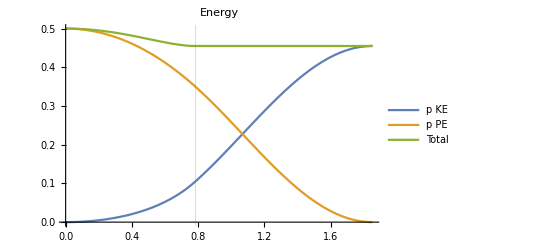
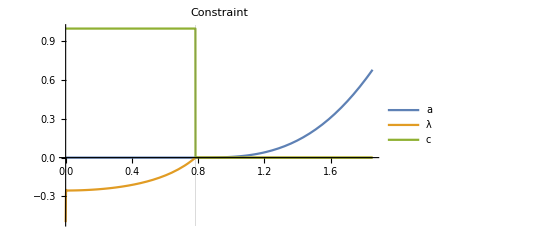
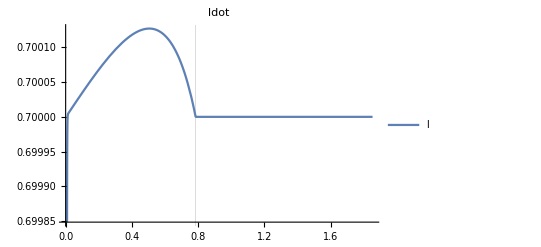
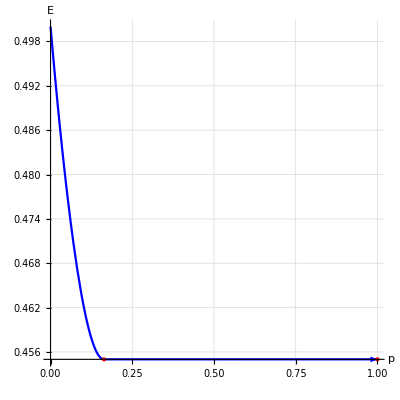

lvel=0.3

Release at t=2.78943

Takeoff at t=3.66124, vel=0.714149

lvel=0.4

Release at t=1.93784

Takeoff at t=2.8481, vel=0.800003

lvel=0.5

Release at t=1.4157

Takeoff at t=2.37003, vel=0.866027

lvel=0.6

Release at t=1.05553

Takeoff at t=2.06172, vel=0.916516

lvel=0.7

Release at t=0.783792

Takeoff at t=1.85307, vel=0.95394

lvel=0.8

Release at t=0.560232

Takeoff at t=1.71025, vel=0.979796

lvel=0.9

Release at t=0.352467

Takeoff at t=1.61688, vel=0.994987

```mathematica
{sr1,velTO1}=runSim[0.7,eoms2,scl,params,0,0];
displaySim[sr1,scl,params,Ep,drawThings]
lvels=Range[0.3,lvelThresh-0.001,0.1];
srs=Table[First@runSim[lvel,eoms2,scl,params,0,0],{lvel,lvels}];
```

```mathematica
(*simAnim[sr1,drawThings,"cl.avi",0.033]*)
```

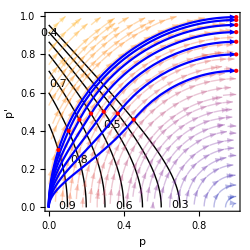

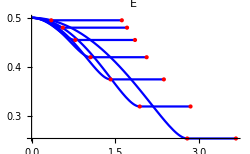

```mathematica
pps=Table[phasePlot[sr,params,Ep,False],{sr,srs}];
ppEs=Table[phasePlot[sr,params,Ep,True],{sr,srs}];
pEs=Table[ePlot[sr,params,Ep],{sr,srs}];


(*eoms1[[-1]]/.{c[t]->1,m->ml α}/.α->0//Simplify*)
Show[Join[{
ContourPlot[lvelforλ0,{pp,0,1},{vp,0,1},
ContourShading->None,
(*ColorFunction->ColorData["GrayTones"],BaseStyle->Directive[Opacity[0.3]],*)
Contours->lvels,ContourLabels->All,FrameLabel->{p,p'}],
(*ContourPlot[1/2m vp^2+V[s[pp]]/.params,{pp,0,1},{vp,0,1},ColorFunction->ColorData["GrayTones"],BaseStyle->Directive[Opacity[0.7]]],*)
StreamPlot[{vp,eact[[1]]/.p[t]->pp}/.params,{pp,0,1},{vp,0,1},StreamStyle->Directive[Red,Opacity[0.3]]]
},pps],
PlotRange->All,ImageSize->250]
(*
Show[Join[{
ContourPlot[lvelforλ0E,{pp,0,1},{Eep,0,1},
ContourShading->None,
Contours->lvels,ContourLabels->All,FrameLabel->{p,Energy}]
},ppEs],
PlotRange->All,ImageSize->250]*)

Show[pEs]
```

```mathematica
(*
(*Approx unlatch time solution (see below*)
unlatcht=(√(R^2-((m R^2 vl^2)/Fs)^(2/3)))/vl/.Fs->k p0/.params;
approxAcc=k p0/m/.params;
stateUL={1/2approxAcc unlatcht^2,approxAcc unlatcht};
ParametricPlot[stateUL,{vl,0.1,2}]*)
```

```mathematica
lvelforλ0E
```

√(2-2 Eep-4 pp+2 pp^2)

```mathematica
(*λforlvel[lv]/.params*)
(*Edot in mode 1*)
pdd1=eoms1[[1,-1]]/.{c[t]->1,ul->0}/.lmode1(*/.{l'[t]->lvelforλ0}*)/.{p'[t]->vp,p[t]->pp}(*/.params*)//Simplify;
pdd1/.m->0//Simplify
Edot1=D[Ep,t]/.p''[t]->pdd1/.{p'[t]->vp,p[t]->pp}(*/.params*)//Simplify;
Edot1/.m->0//Simplify
(*ContourPlot[Edot1/.lv->0.5,{pp,0.1,1},{vp,0,1}]*)
Plot[pdd1,{pp,0,1}]
```

(-k (p0-pp) pp (pp-2 R)+ml (-pp+R) (vp^2+l'[t]^2))/(ml (pp-R)^2)

-k (p0-pp) vp

-Graphics-

### 3. Round latch new analysis

```mathematica
(*NEW ANALYSIS: Last row of MAinv*)
e3TMAi={(2 ml R-2 ml p[t])/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2),-(2 m l[t])/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2),(m ml)/(-4 ml R^2-4 m l[t]^2+8 ml R p[t]-4 ml p[t]^2)};
(e3TMAi.{-g,0,-dAdq}/.m->ϵ ml/.ml->m/ϵ)(*/.ϵ->0*)//Simplify
(*D[D[aa,{q}],t].dq//Simplify
D[aa,{q}].dq//Simplifyz
aa//Simplify
lv/.Last@Solve[λforlvel[lv]==0,lv]*)
(*Plot[vl^2/(R(1-v*)
```

(dAdq m+2 g R-2 g p[t])/(4 (ϵ l[t]^2+(R-p[t])^2))

Sym inverse {(-R+p[t])/(2 (ϵ l[t]^2+(R-p[t])^2)),(ϵ l[t])/(2 (ϵ l[t]^2+(R-p[t])^2)),-m/(4 (ϵ l[t]^2+(R-p[t])^2))} vs. new {-(2 (R-p[t]))/m,(2 l[t])/ml}

k (-p0+p[t])

Check with constraint Hessian 0

Unlatch evt = -2 vl^2-(2 t^2 vl^4)/(R^2-t^2 vl^2)+(2 k √(R^2-t^2 vl^2) (p0-R+√(R^2-t^2 vl^2)))/m

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

2.81456

7.62052

0.423174

1.51644

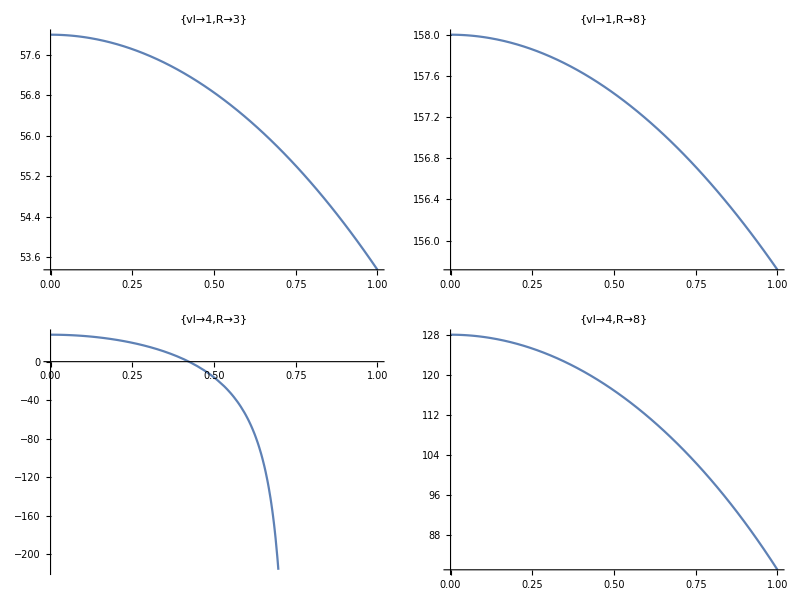
(-Graphics-)

```mathematica
(*NEW NEW*)
Ap=Ma[[3,1]];
Al=Ma[[3,2]];
Aa=Ma[[3,1;;2]];
Print["Sym inverse ",(e3TMAi(*.{-g,0,-dAdq}*)/.m->ϵ ml/.ml->m/ϵ)(*/.ϵ->0*)//Simplify," vs. new ",
(*Analytically invert, leave out scalar α*)
Ma[[3,1;;2]].DiagonalMatrix[{1/m,1/ml}]];

(*m,p0=Δx,k exactly from latch paper. E0 is a metamaterial param TODO.*)
params2={m->1000,Fs->1000*10,p0->10,k->1000,vlMAX->10(*,E0->3000000*)};

HOOKE=True;
G=If[HOOKE,D[V[scl[p[t]]],{p[t]}],-Fs]
(*General version*)
Print["Check with constraint Hessian ",D[Aa,t].dq-dq.D[Aa,{q}].dq//Simplify];
unlatchingSubs=Join[First@Solve[Aa.dq==0,p'[t]],First@Solve[aa==0,p[t]]];
Print["Unlatch evt = ",unlatchEvt=((Ap/m G-D[Aa,t].dq)//.unlatchingSubs/.{l'[t]->vl,l[t]->vl t})//Simplify];
(*The Min is more correct but makes it non-smooth, and the result for HOOKE seems the same with or without*)
unlatchtsol=(*Min[*)Re[t/.Solve[unlatchEvt==0,t][[4]]](*,R/vl]*);

(*Test unlatch event*)
testPlotEvt[subs_]:=Module[{tul=unlatchtsol/.params2/.subs},
Print[tul//N];
Plot[unlatchEvt/.subs/.params2,{t,0,1},GridLines->{{tul},None},PlotLabel->subs]
];
Table[testPlotEvt[{vl->vli,R->Ri}],{vli,{1,4}},{Ri,{3,8}}]//MatrixForm
(*This makes sense; bigger latch takes longer for the same *)
```

```mathematica
(*analytical assuming constant Fs*)
unlatchtsolA1 =1/vl Sqrt[R^2-(m vl^2R^2/Fs)^(2/3)];
unlatchtsolA =Re[unlatchtsolA1];
```

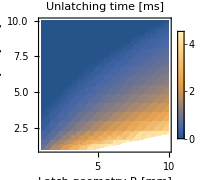

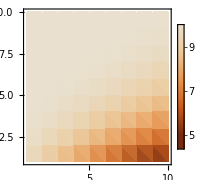
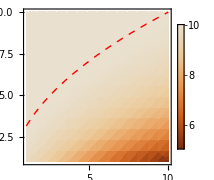

C:\Users\Wyss User\Downloads\control_paper_sims\unlatch2.png

```mathematica
(*Fully analytical expression for the unlatching state*)
unlatchState={p[t],p'[t]}//.unlatchingSubs/.{l'[t]->vl,l[t]->vl tul};

(*Try to replicate the heatmap from the latch presentation*)
unlatchE=Sqrt[2*(1/2 m unlatchState[[2]]^2+V[scl[unlatchState[[1]]]])/m];

Eexact[R1_,vl1_]:=(unlatchE/.params2/.{tul->unlatchtsol/.{R->R1,vl->vl1}/.params2})/.{R->R1,vl->vl1}/.params2
(*ContourPlot[R/vl,{

R,1,10},{vl,1,10},FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},PlotLegends->Automatic,PlotLabel->"Unlatching time [ms]"],*)
DensityPlot[unlatchtsolA/.params2,{R,1,10},{vl,1,10},FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},PlotLegends->Automatic,PlotLabel->"Unlatching time [ms]",ImageSize->Small]
Row@{ListDensityPlot[Flatten[Table[{R1,vl1,Eexact[R1,vl1]},{R1,1,10},{vl1,1,10}],1],(*FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},*)PlotLegends->Automatic,(*PlotLabel->"vTO [m/s]",*)ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"SiennaTones",{5,10}}]],
Show[{
DensityPlot[unlatchE/.tul->unlatchtsolA/.params2,{R,1,10},{vl,1,10},(*FrameLabel->{"Latch geometry R [mm]","Latch velocity vl [m/s]"},*)PlotLegends->Automatic,(*PlotLabel->"vTO [m/s]",*)ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"SiennaTones",{5,10}}]],
ContourPlot[unlatchtsolA1/.params2,{R,1,10},{vl,1,10},ContourShading->None,Contours->{0.01},ContourStyle->Directive[Dashed,Red]]
}]
}
Export[NotebookDirectory[]<>"unlatch2.png",%,ImageResolution->200]
```

#### Hooke-like standard spring

```mathematica
(*NOTE: normalizing by release energy. unlatchState, unlatchtsolA1 both indep of p0. Only Fs has p0 in it.*)
```

-Graphics-

1/5 Re[√(R^2-(-(2^(-4+n) 5^(-3+n) m (-p0)^(1-n) R^2)/n)^(2/3))]

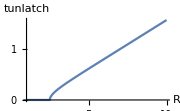

```mathematica
(*Design space simplified*)
(*Normalized so that the total energy stored at p=0 is the same*)
V2[s_,n_]:=1/2knorm s^n/.({knorm->k p0^(2-n)}/.params2);
(*Would like an expression for the max potential energy that can be converted to KE, as a func of ζ as well*)
(*χ[t]/.First@DSolve[χ''[t]+2ζ ωn χ'[t]+ωn^2 χ[t]==0,χ,t]//Simplify*)
(*http://web.mst.edu/~stutts/SupplementalNotes/EqivalentViscousDamping.pdf*)
(*kd ω^2X^2Integrate[Cos[ω t-ϕo]^2,{t,0,π/(2ω)}]/.{ϕo->π/2,kd->2 ζ ω,X->p0}*)
Clear[Wd];
Wd[s_,ζ_]:=2ζ ω^3(p0-s)^2Integrate[Cos[x]^2,{x,0,π/2}]/.{ω->Sqrt[k/m]}
V2rel[s_,n_,ζ1_]:=V2[s,n]-Wd[s,ζ1]

(*Cannot get instantaneous release (assume finite latch power), especially at higher R*)
minUnlatchTime=unlatchtsolA/.{Fs->-(D[V2[scl[p],n],p]/.p->0),vl->5}
(*Limit[unlatchtsolA,vl->0]*)
Plot[minUnlatchTime/.n->2/.params2,{R,1,10},ImageSize->Small,AxesLabel->{R,tunlatch}]
Emin=V2rel[-scl[R],n,(*ζ*)10];
unlatchE2=(1/2 m unlatchState[[2]]^2+V2rel[-scl[unlatchState[[1]]],n,(*ζ*)0])/.params2;
Emax=unlatchE2/.{tul->minUnlatchTime,vl->vlMAX}/.params2;
```

```mathematica
(*Check how to pick ζ for Emin, Emax for NOR. FIXME need better formula with ζ. *)
(*Plot[Evaluate[{Emin(*,Emax*)}/.params2/.{R->5,n->2}],{ζ,0,10}]*)
(*Functions for release energy*)
Efinalns[R1_,n_,vl1_,ζ_]:=((1/2 m unlatchState[[2]]^2+V2(*rel*)[-scl[unlatchState[[1]]],n(*,ζ*)])/.tul->unlatchtsolA1/.{Fs->-(D[V2[-scl[p],n],p]/.p->0)})/.{vl->vl1,R->R1}/.params2;
(*Min w.r.t. vL*)
EminvLns[R1_,n_,ζ_]:=V2rel[-scl[R1],n,ζ]/.params2;
(*
nsEWrtControl[R1_,n1_]:=ContourPlot[Efinalns[R1,n1,vl,ζ],{vl,0.001,10},{ζ,0,10},FrameLabel->{"vl","ζ"},PlotLegends->Automatic,FrameLabel->{"vL","ζ"},PlotLegends->Automatic,PlotLabel->"R="<>ToString[R1]<>",n="<>ToString[n1],ImageSize->Small]
Grid@{{nsEWrtControl[3,1.8],nsEWrtControl[8,1.8]},{nsEWrtControl[3,2.2],nsEWrtControl[8,2.2]}}*)
(*Emax bottom right, Emin top left*)
```

Test: 0.75

Test: 0.795507

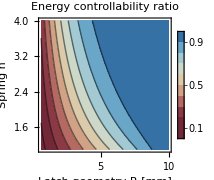
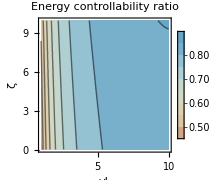
-Graphics- | -Graphics-

C:\Users\Wyss User\Downloads\control_paper_sims\Figure5A.pdf

```mathematica
(*So, w.r.t. design, pick top right for Emax, bottom left for Emin*)
nsNORWrtDesign[]:=Module[{Emax=(*Efinalns[R,n,15,0]*)V2[p0,2]/.params2,Emin=EminvLns[R,n,(*10*)0]},
Print["Test: ",(Emax-Emin)/Emax/.params2/.{R->5,n->2}//N];
Show[{
ContourPlot[(Emax-Emin)/Emax/.params2,{R,0.6,10},{n,1.1,4},FrameLabel->{"Latch geometry R [mm]","Spring n"},PlotLegends->Automatic,PlotLabel->"Energy controllability ratio",ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"RedBlueTones",{0.2,1}}]](*,
ContourPlot[minUnlatchTime/.params2,{R,1,10},{ar,0.2,1},ContourShading->None,Contours->{0.1},ContourStyle->Directive[Dashed,Red]]*)
}]
];
(*NOR w.r.t. control, seems from the 4 plots above that Emax for small R, large ar, Emin for large R, small ar*)
nsNORWrtControl[]:=Module[{Emax=Efinalns[7,3,vl,ζ],Emin=EminvLns[7,1.5,ζ]},
Print["Test: ",(Emax-Emin)/Emax/.params2/.{vl->5,ζ->1}//N];
Show[{
ContourPlot[(Emax-Emin)/Emax/.params2,{vl,1,10},{ζ,0,10},FrameLabel->{"vL","ζ"},PlotLegends->Automatic,PlotLabel->"Energy controllability ratio",ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"RedBlueTones",{0.2,1}}]](*,
ContourPlot[minUnlatchTime/.params2,{R,1,10},{ar,0.2,1},ContourShading->None,Contours->{0.1},ContourStyle->Directive[Dashed,Red]]*)
}]
];
Grid@{{
nsNORWrtDesign[],nsNORWrtControl[]}}
Export[NotebookDirectory[]<>"Figure5A.pdf",%]
```

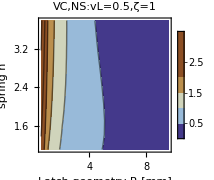
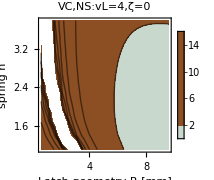
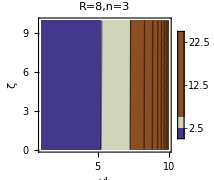
-Graphics- | -Graphics- | -Graphics-

C:\Users\Wyss User\Downloads\control_paper_sims\Figure6A.pdf

```mathematica
nsStabWrtDesign[vL1_,ζ1_]:=ListContourPlot[Flatten[Table[{R,n,Re[dvldp02/.{vl->vL1,ζ->ζ1}]},{R,0.6,10,0.5},{n,1.1,4,0.3}],1],FrameLabel->{"Latch geometry R [mm]","spring n"},PlotLegends->Automatic,PlotLabel->"VC,NS:vL="<>ToString[vL1]<>",ζ="<>ToString[ζ1],ImageSize->Small,ColorFunctionScaling->False,ColorFunction->Function[{x},Reverse@ColorData[{"RedBlueTones",{0,2}}][x]]]
Grid@{{nsStabWrtDesign[0.5,1],nsStabWrtDesign[4,0],nsStabWrtControl[8,3]}}
(*mmStabWrtDesign[10,0]*)
Export[NotebookDirectory[]<>"Figure6A.pdf",%]
```

```mathematica
Eul/.ζ->0
V2rel[scl[unlatchState[[1]]],n,ζ]
```

2^(4-n) 5^(5-n) (p0-R+((2^(-4+n) 5^(-5+n) m p0^(1-n) R^2 vl^2)/n)^(1/3))^n+(m vl^2 (R^2-((2^(-4+n) 5^(-5+n) m p0^(1-n) R^2 vl^2)/n)^(2/3)))/(2 ((2^(-4+n) 5^(-5+n) m p0^(1-n) R^2 vl^2)/n)^(2/3))

2^(4-n) 5^(5-n) (-p0+R-√(R^2-tul^2 vl^2))^n-1/2 (k/m)^(3/2) π (2 p0-R+√(R^2-tul^2 vl^2))^2 ζ

```mathematica
EulRHooke=0.001*(Eul/.params2/.n->2);
```

#### Metamaterial spring

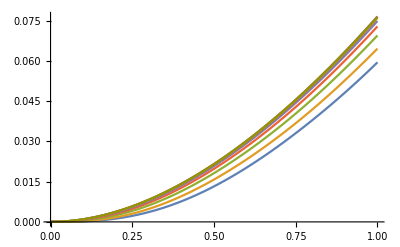
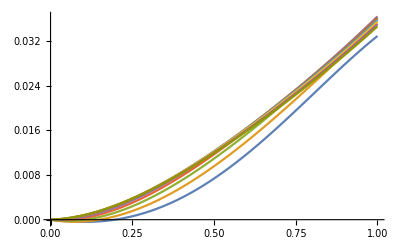

```mathematica
(*For metamaterial spring*)
c1=Interpolation[{{0.1,0.0019},{0.2,0.0046},{0.3,0.0352},{0.4,0.0631},{0.5,0.0837},{0.6,0.0948},{0.7,0.0987},{0.8,0.1010},{0.9,0.1008},{1.0,0.1007}}];
c2=Interpolation[{{0.1,0.1785},{0.2,0.2714},{0.3,0.1947},{0.4,0.1030},{0.5,0.0294},{0.6,-0.0119},{0.7,-0.0275},{0.8,-0.0366},{0.9,-0.0363},{1.0,-0.0363}}];
c3=Interpolation[{{0.1,-0.1847},{0.2,-0.4553},{0.3,-0.3615},{0.4,-0.2180},{0.5,-0.0961},{0.6,-0.0259},{0.7,0.0012},{0.8,0.0170},{0.9,0.0169},{1.0,0.0168}}];
c4=Interpolation[{{0.1,0.0638},{0.2,0.3432},{0.3,0.2873},{0.4,0.1797},{0.5,0.0843},{0.6,0.0286},{0.7,0.0068},{0.8,-0.0059},{0.9,-0.0058},{1.0,-0.0058}}];
c5=Interpolation[{{0.1,0.0},{0.2,-0.0993},{0.3,-0.0862},{0.4,-0.0549},{0.5,-0.0264},{0.6,-0.0095},{0.7,-0.0028},{0.8,0.0010},{0.9,0.0010},{1.0,0.0010}}];
mmΦs2[ϵ_,ar_]:=E0(c1[ar]ϵ^2+c2[ar]ϵ^3+c3[ar]ϵ^4+c4[ar]ϵ^5+c5[ar]ϵ^6)
(*Note at 0.1 have different signs so the fitting is weird*)
d1=Interpolation[{{0.1,-0.00733},{0.2,-0.01010},{0.3,-0.00822},{0.4,-0.00501},{0.5,-0.00213},{0.6,-0.00011},{0.7,0.00106},{0.8,0.00154},{0.9,0.00158},{1.0,0.00231}}];
d2=Interpolation[{{0.1,0.02932},{0.2,0.07198},{0.3,0.08441},{0.4,0.08285},{0.5,0.07732},{0.6,0.07203},{0.7,0.06825},{0.8,0.06623},{0.9,0.06491},{1.0,0.06140}}];
d3=Interpolation[{{0.1,0.04836},{0.2,-0.0271},{0.3,-0.05667},{0.4,-0.06246},{0.5,-0.05970},{0.6,-0.05535},{0.7,-0.05183},{0.8,-0.05007},{0.9,-0.04834},{1.0,-0.04422}}];
d4=Interpolation[{{0.1,-0.03742},{0.2,0.00036},{0.3,0.01663},{0.4,0.02106},{0.5,0.02088},{0.6,0.01953},{0.7,0.01829},{0.8,0.01774},{0.9,0.01693},{1.0,0.01518}}];
(*This is the dynamic recoil (max energy that can be extracted. Use this to predict the release energy. (2) from Xudong*)
mmΦv2[ϵ_,ar_]:=E0(d1[ar]ϵ+d2[ar]ϵ^2+d3[ar]ϵ^3+d4[ar]ϵ^4)
(*Confirm by comparing to Xudong plots*)
{
Plot[Evaluate@Table[mmΦs2[ϵ,ar]/E0,{ar,0.1,1,0.1}],{ϵ,0,1}],
Plot[Evaluate@Table[mmΦv2[ϵ,ar]/E0,{ar,0.1,1,0.1}],{ϵ,0,1}]
}

(*Normalization*)
Edes=V2[scl[0],2]/.params2;
(*Pick Ly by setting ar=0.5,ϵ=0.5 energy to Edes. Choose h*Lx*Ly=10^(-3)Ly, E0=3*10^6 (mN/mm^2)=3GPa. k=1 since essentially we choose Ly/k through this*)
(*1/2 k dL^2/(E0 Ly Lx h)/.{h->10^(-2)Ly,Lx->0.1Ly,dL->ϵ Ly,k->1}*)
Lyref=(Edes/(0.1*0.01*mmΦs2[ϵ,ar]/.{ar->0.5,ϵ->0.5,E0->3*10^6}))^(1/3);
(*^ checked the above, matches Patrick MATLAB file*)

(*Get mm spring strain ϵ as a func of projectile position p. For NS scl[p]=p-p0*)
smmϵ[ar_,p_]:=Module[{ϵinit},
ϵinit=First@Solve[(mmΦs2[ϵ,ar]/.E0sol)==Edes&&ϵ>0&&ϵ<1,ϵ];
(*p=0=>ϵ=ϵinit. p > 0 => ϵinit small => p0 small etc. See diagram in notes.*)
Max[Min[(ϵ/.ϵinit)-p/Lyref,0.9],0.1]
];
E0sol={E0->3*10^6};
```

```mathematica
(*Also including the α parameter. Eqns (3) (4) from Xudong*)
Vmm[p_,ar_,α_]:=(1+α)mmΦs2[smmϵ[ar,p],ar]
Vmmrel[p_,ar_,α_]:=mmΦv2[smmϵ[ar,p],ar]+α mmΦs2[smmϵ[ar,p],ar]
(*Working normalization: Energy=Edes for each ar at p=0*)
Table[Vmm[0,ar,0]/.E0sol,{ar,0.1,1,0.1}]
```

{50000.,50000.,50000.,50000.,50000.,50000.,50000.,50000.,50000.,50000.}

```mathematica
Finitialmm[ar_,α_]:=(-D[Vmm[p,ar,α],p]/.p->0/.E0sol)
Finitialmm[0.3,0]
Finitialmm[0.7,0.5]
```

23078.8

34816.5

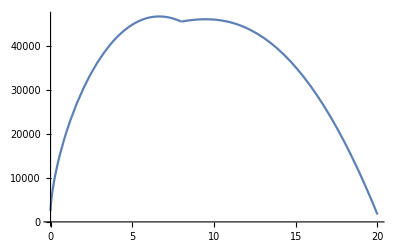
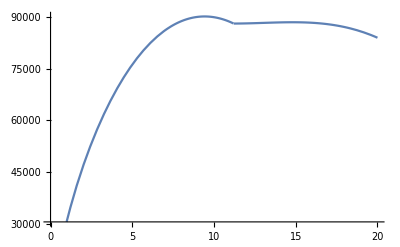

```mathematica
(*Normalization*)
(*Plot[{Legended[V2[scl[p],2]/.params2,"Hooke"],Legended[Vmm[scl[p],0.1,0]/.params2,"MM 0.1"],Legended[Vmm[scl[p],1.0,0]/.params2,"MM 1.0"]},{p,0,10},AxesLabel->{p,"Spring energy"},ImageSize->Small]*)
(*Export[NotebookDirectory[]<>"mmnorm.pdf",%]*)

(*Functions for release energy*)
Efinalmm[R1_,ar_,vl1_,α_]:=Module[{},
((1/2 m unlatchState[[2]]^2+Vmmrel[unlatchState[[1]],ar,α])/.tul->unlatchtsolA1/.{Fs->Finitialmm[ar,α]})/.{vl->vl1,R->R1}/.params2/.E0sol
];
(*Validation: higher vL does not necessarily mean higher final energy in mm*)
{
Plot[Efinalmm[9,0.7,vl,0.1],{vl,0,20}],
Plot[Efinalmm[10,0.3,vl,1],{vl,0,20}]
}
(*FindMaximum[Efinalmm[10,0.3,vl,0.5],{vl,10},AccuracyGoal->2]*)
(*(*Min w.r.t. vL*)
EminvLmm[R1_,ar_,α_]:=Vmmrel[R1,ar,α]/.params2;
(*Cannot get instantaneous release (assume finite latch power), especially at higher R. Use the static one for unlatching*)
minUnlatchTime=unlatchtsolA/.{Fs->-(D[Vmm[p,ar,α],p]/.p->0),vl->vlMAX};*)
```

```mathematica
(*mmEWrtControl[R1_,ar1_]:=ContourPlot[0.001*Efinalmm[R1,ar1,vl,α]/.params2,{vl,0.001,10},{α,0,1},FrameLabel->{"vl","α"},PlotLegends->Automatic,FrameLabel->{"vL","α"},PlotLegends->Automatic,PlotLabel->"R="<>ToString[R1]<>",ar="<>ToString[ar1],ImageSize->Small]
Grid@{{mmEWrtControl[5,0.2],mmEWrtControl[8,0.2]},{mmEWrtControl[5,1],mmEWrtControl[8,1]}}*)
(*Emax top right, Emin bottom left*)
```

0.980306

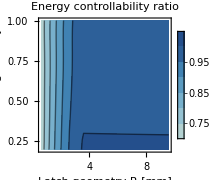

C:\Users\Wyss User\Downloads\control_paper_sims\Figure5B.pdf

```mathematica
(*So, w.r.t. design, pick top right for Emax, bottom left for Emin. Plots above: vl for max energy~=11*)
mmNOR[R_,ar_]:=Module[{Emax=FindMaximum[Efinalmm[R,ar,vl,1],{vl,10},AccuracyGoal->2][[1]],Emin=Efinalmm[R,ar,0.001,0]},
(Emax-Emin)/Emax
];
mmNOR[5,0.5]
mmNORWrtDesign[]:=ListContourPlot[Flatten[Table[{R,ar,mmNOR[R,ar]},{R,0.6,10,0.5},{ar,0.2,1,0.05}],1],FrameLabel->{"Latch geometry R [mm]","Metamaterial geometry ar"},PlotLegends->Automatic,PlotLabel->"Energy controllability ratio",ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"RedBlueTones",{0.2,1}}]]
(*NOR w.r.t. control, seems from the 4 plots above that Emax for small R, large ar, Emin for large R, small ar*)
(*mmNORWrtControl[]:=Module[{Emax=Efinalmm[7,0.1,vl,α],Emin=EminvLmm[7,1,α]},
Print["Test: ",(Emax-Emin)/Emax/.params2/.{vl->5,α->0.5}];
Show[{
ContourPlot[(Emax-Emin)/Emax/.params2,{vl,1,10},{α,0,1},FrameLabel->{"vL","α"},PlotLegends->Automatic,PlotLabel->"Energy controllability ratio",ImageSize->Small,ColorFunctionScaling->False,ColorFunction->ColorData[{"RedBlueTones",{0.2,1}}]](*,
ContourPlot[minUnlatchTime/.params2,{R,1,10},{ar,0.2,1},ContourShading->None,Contours->{0.1},ContourStyle->Directive[Dashed,Red]]*)
}]
];*)
Grid@{{
mmNORWrtDesign[](*,mmNORWrtControl[]*)}}
Export[NotebookDirectory[]<>"Figure5B.pdf",%]
```

```mathematica
EulRMM=0.001*(Eul/.params2/.ar->0.5);
```